```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## Import Data

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
Vdata=SplitBy[Import["latticedata/AllData2p1Flavors/Vall.txt","Table"],First];

ReVdataT[n_]:=Table[Vdata[[n,x,2;;3]],{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataT[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ReVdataTe[n_]:=Table[Vdata[[n,x,2;;4]],{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataTe[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]],Vdata[[n,x,6]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ReVdataTn[n_]:=ReVdataT[n]/.{a_,b_}:>{a/0.197327,b};
ImVdataTn[n_]:=ImVdataT[n]/.{a_,b_}:>{a/0.197327,b};
ReVdataTne[n_]:=ReVdataTe[n]/.{a_,b_,c_}:>{a/0.197327,b,c};
ImVdataTne[n_]:=ImVdataTe[n]/.{a_,b_,c_}:>{a/0.197327,b,c};

T0data=Join[{Import["latticedata/LowTemp/OlafPotentialLinesTmax12PotentialT41.05.dat","Table"][[All,1;;3]]},{Import["latticedata/LowTemp/OlafPotentialLinesTmax12PotentialT71.54.dat","Table"][[All,1;;3]]}];
T0datan=T0data/.{a_,b_,c_}:>{a/0.197327,b,c};
```

## Define functions for real part

```mathematica
ReV[r_,m_,α_,σ_,c_,d_,f_]:=-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c-(5^(4/5) d^(3/5)  α^(2/5) Gamma[2/5])/(Gamma[-2/5] m^(4/5))+(d^(4/5)α^(1/5)(2 5^(2/5))/(Gamma[-2/5] m^(2/5)))r BesselK[2/5,2/5 r^(5/2)(m^2 d/α)^(1/2)]-(2 m^4 f^3)/α^2 BesselK[2,2 (m^2 f/α)^(1/2) r^(1/2)]/((m^2 f/α) r);
ReVo[r_,m_,α_,σ_,c_]:=-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c;
ReVm0[r_,α_,σ_,c_,d_,f_]:=c-α/r-f/r^2+σ r+d r^2;
ReVm00[r_,α_,σ_,c_]:=c-α/r+σ r;
```

```mathematica
(*-3((√(α e))/m)Exp[-1/3(m^2 e/α)^(1/2)r^3+(3 √(α e))/m] for a=3*)
```

```mathematica
Vsb[r_,α_,σ_,c_,d_,f_]:=HeavisideTheta[1.25/0.197-r](c-α/r-f/r^2+σ r+d r^2)+HeavisideTheta[r-1.25/0.197](c-α/(1.25/0.197)-f/(1.25/0.197)^2+σ 1.25/0.197+d(1.25/0.197)^2);
```

```mathematica
Assuming[r∈Reals&&r>0&&d∈Reals&&d>0&&α∈Reals&&α>0&&m∈Reals&&f∈Reals&&f>0,Limit[ReV[r,m,α,σ,c,d,f],m->0]]
```

c-f/r^2+d r^2-α/r+r σ

## Low T Cornell Fitting & Interpolation

```mathematica
T0datarand[n_]:=Table[{T0data[[n]][[i,1]],RandomVariate[NormalDistribution[T0data[[n]][[i,2]],T0data[[n]][[i,3]]]]},{i,Length[T0data[[n]]]}]
```

### beta = 6.9 Fitting

```mathematica
VaryFitLow=Range[2,4];
VaryFitHigh=Range[20,28];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];

VaryFitLowAR={2,2,2,2,2,1,3,1,3}+1;
VaryFitHighAR={24,28,26,30,22,24,24,26,22}-2;
```

#### Varied Weights (not in use)

{0.449955,0.0207984}

{0.223087,0.00686867}

{1.75543,0.0257048}

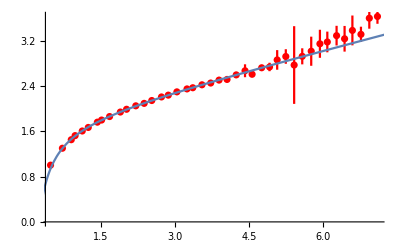

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.437304,0.0639055}

{0.230147,0.0267482}

{1.7356,0.088547}

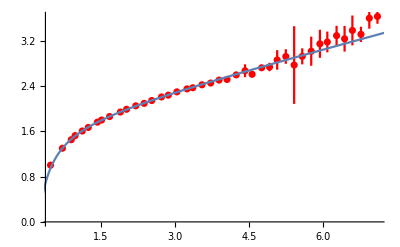

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]]),VarianceEstimatorFunction->(1&)];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.449955,0.0207984}

{0.223087,0.00686867}

{1.75543,0.0257048}

-Graphics-

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2,VarianceEstimatorFunction->(1&)];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.437304,0.0639055}

{0.230147,0.0267482}

{1.7356,0.088547}

-Graphics-

#### Use this one!

```mathematica
αfit69r={};
σfit69r={};
cfit69r={};
dfit69r={};
efit69r={};
ffit69r={};
SetSharedVariable[αfit69r,σfit69r,cfit69r,dfit69r,efit69r];
ParallelDo[Module[{fit0,fit,al0,sig0,const0},fit0=NonlinearModelFit[T0datarand[1][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm00[r,al,sig,const],{al,sig,const},r];
al0=al/.fit0["BestFitParameters"];
sig0=sig/.fit0["BestFitParameters"];
const0=const/.fit0["BestFitParameters"];fit=NonlinearModelFit[T0datarand[1][[VaryFit[[i,1]];;VaryFit[[i,2]]]],{ReVm00[r,al,sig,const],0.9 al0<al<1.1 al0,0.9 sig0<sig<1.1 sig0},{{al,al0},{sig,sig0},{const,const0}},r];
αfit69r=Append[αfit69r,al/.fit["BestFitParameters"]];
σfit69r=Append[σfit69r,sig/.fit["BestFitParameters"]];
cfit69r=Append[cfit69r,const/.fit["BestFitParameters"]]
(*dfit69r=Append[dfit69r,const1/.fit["BestFitParameters"]];*)
(*efit69r=Append[efit69r,const2/.fit["BestFitParameters"]];*)
(*ffit69r=Append[ffit69r,const2/.fit["BestFitParameters"]];*)];,{ii,1,100},{i,1,Length[VaryFit]}]
αfinal69r={Mean[αfit69r],StandardDeviation[αfit69r]}
σfinal69r={Mean[σfit69r],StandardDeviation[σfit69r]}
cfinal69r={Mean[cfit69r],StandardDeviation[cfit69r]}
(*dfinal69r={Mean[dfit69r],StandardDeviation[dfit69r]}*)
(*efinal69r={Mean[efit69r],StandardDeviation[efit69r]}*)
(*ffinal69r={Mean[ffit69r],StandardDeviation[ffit69r]}*)
```

{0.471242,0.0420996}

{0.217107,0.0129385}

{1.78111,0.0500451}

```mathematica
αfinal69r={0.4710512623279609,0.04708158386118884}(*run with 10k points, all varied fitting*)
```

{0.471051,0.0470816}

```mathematica
σfinal69r={0.21706712111822668,0.015928132568206174}
```

{0.217067,0.0159281}

```mathematica
cfinal69r={1.7808043891992207,0.059392193900140486}
```

{1.7808,0.0593922}

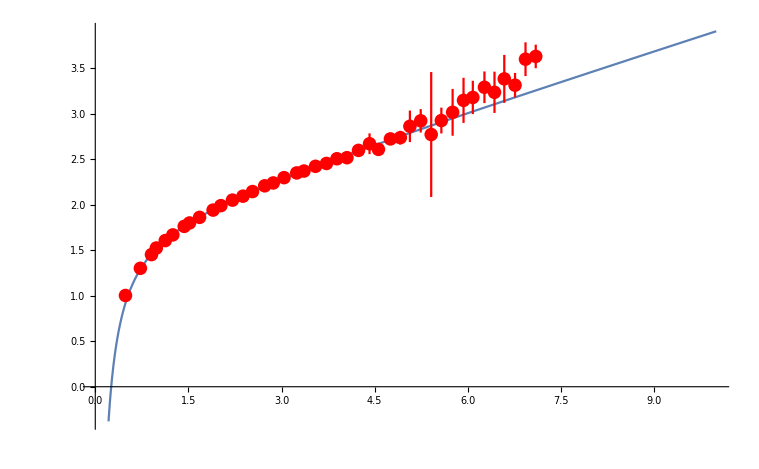

```mathematica
Show[{Plot[ReVm00[r,αfinal69r[[1]],σfinal69r[[1]],cfinal69r[[1]]],{r,0.01,10}],ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All]}]
```

### beta = 7.4 Fitting

```mathematica
VaryFitLow=Range[5,7];
VaryFitHigh=Range[26,34];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];
```

```mathematica
VaryFitLowAR={2,2,2,2,2,1,3,1,3}+4;
VaryFitHighAR={24,28,26,30,22,24,24,26,22}+4;
```

#### Varied Weights (not in use)

{0.386026,0.00681763}

{0.264172,0.003189}

{2.65021,0.00972345}

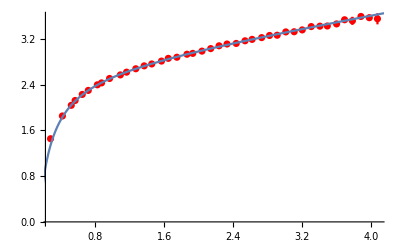

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.389033,0.00967473}

{0.263519,0.00430806}

{2.65451,0.0135868}

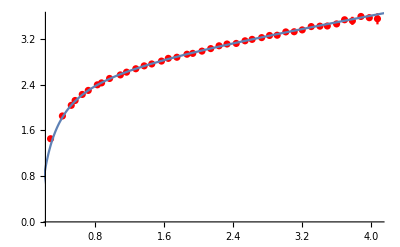

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]]),VarianceEstimatorFunction->(1&)];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.386026,0.00681763}

{0.264172,0.003189}

{2.65021,0.00972345}

-Graphics-

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2,VarianceEstimatorFunction->(1&)];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.389033,0.00967473}

{0.263519,0.00430806}

{2.65451,0.0135868}

-Graphics-

#### Use this one!

```mathematica
αfit748r={};
σfit748r={};
cfit748r={};
dfit748r={};
efit748r={};
ffit748r={};
SetSharedVariable[αfit748r,σfit748r,cfit748r,dfit748r,efit748r];
ParallelDo[Module[{fit0,fit,al0,sig0,const0},fit0=NonlinearModelFit[T0datarand[2][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm00[r,al,sig,const],{al,sig,const},r];
al0=al/.fit0["BestFitParameters"];
sig0=sig/.fit0["BestFitParameters"];
const0=const/.fit0["BestFitParameters"];fit=NonlinearModelFit[T0datarand[2][[VaryFit[[i,1]];;VaryFit[[i,2]]]],{ReVm00[r,al,sig,const],0.9 al0<al<1.1 al0,0.9 sig0<sig<1.1 sig0},{{al,al0},{sig,sig0},{const,const0}},r];
αfit748r=Append[αfit748r,al/.fit["BestFitParameters"]];
σfit748r=Append[σfit748r,sig/.fit["BestFitParameters"]];
cfit748r=Append[cfit748r,const/.fit["BestFitParameters"]]
(*dfit748r=Append[dfit748r,const1/.fit["BestFitParameters"]];*)
(*efit748r=Append[efit748r,const2/.fit["BestFitParameters"]];*)
(*ffit748r=Append[ffit748r,const2/.fit["BestFitParameters"]];*)];,{ii,1,100},{i,1,Length[VaryFit]}]
αfinal748r={Mean[αfit748r],StandardDeviation[αfit748r]}
σfinal748r={Mean[σfit748r],StandardDeviation[σfit748r]}
cfinal748r={Mean[cfit748r],StandardDeviation[cfit748r]}
(*dfinal748r={Mean[dfit748r],StandardDeviation[dfit748r]}*)
(*efinal748r={Mean[efit748r],StandardDeviation[efit748r]}*)
(*ffinal748r={Mean[ffit748r],StandardDeviation[ffit748r]}*)
```

{0.372697,0.0123713}

{0.271234,0.0120751}

{2.62876,0.0266216}

```mathematica
αfinal748r={0.38421689,0.0267250638}(*run with 10k points, all varied fitting*)
```

{0.471051,0.0470816}

```mathematica
σfinal748r={0.26496115,0.0142910265}
```

{0.217067,0.0159281}

```mathematica
cfinal748r={2.646969377,0.041757844}
```

{1.7808,0.0593922}

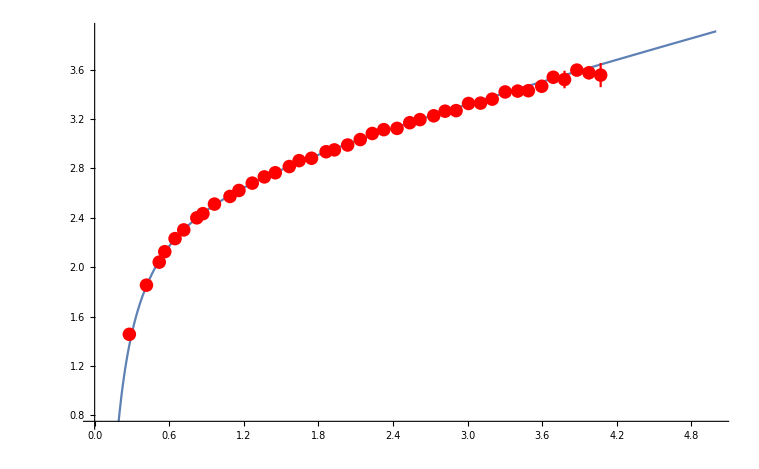

```mathematica
Show[{Plot[ReVm00[r,αfinal748r[[1]],σfinal748r[[1]],cfinal748r[[1]]],{r,0.01,5}],ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All]}]
```

### Linear Interpolation

```mathematica
β={6.8,6.9,7,7.125,7.25,7.3,7.48};
T={0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861};
```

```mathematica
btinter=Interpolation[Transpose[{T,β}]];
btinter1=Interpolation[Transpose[{T,β}],InterpolationOrder->1];
```

```mathematica
beta2T0res={αfinal69r,σfinal69r,cfinal69r};
beta7T0res={αfinal748r,σfinal748r,cfinal748r};
```

```mathematica
T0constfit={LinearModelFit[{{β[[2]],beta2T0res[[1,1]]},{β[[7]],beta7T0res[[1,1]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[2,1]]},{β[[7]],beta7T0res[[2,1]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[3,1]]},{β[[7]],beta7T0res[[3,1]]}},x,x]};
T0errfit={LinearModelFit[{{β[[2]],beta2T0res[[1,2]]},{β[[7]],beta7T0res[[1,2]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[2,2]]},{β[[7]],beta7T0res[[2,2]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[3,2]]},{β[[7]],beta7T0res[[3,2]]}},x,x]};
```

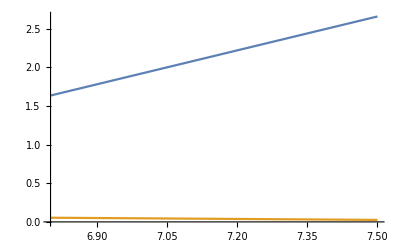

```mathematica
Plot[{T0constfit[[3]][x],T0errfit[[3]][x]},{x,6.8,7.5}]
```

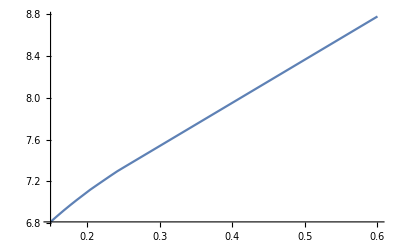

```mathematica
Plot[btinter1[x],{x,0.15,0.6}]
```

```mathematica
Table[T0constfit[[2]][β[[i]]],{i,1,Length[β]}]
```

{0.207775,0.217107,0.22644,0.238105,0.24977,0.254436,0.271234}

```mathematica
Table[T0errfit[[2]][β[[i]]],{i,1,Length[β]}]
```

{0.0130873,0.0129385,0.0127896,0.0126035,0.0124175,0.012343,0.0120751}

```mathematica
Tscanc=Table[i,{i,0.15,0.25,0.003}]
```

{0.15,0.153,0.156,0.159,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249}

```mathematica
Tscanb=Table[i,{i,0.15,0.6,0.005}]
```

{0.15,0.155,0.16,0.165,0.17,0.175,0.18,0.185,0.19,0.195,0.2,0.205,0.21,0.215,0.22,0.225,0.23,0.235,0.24,0.245,0.25,0.255,0.26,0.265,0.27,0.275,0.28,0.285,0.29,0.295,0.3,0.305,0.31,0.315,0.32,0.325,0.33,0.335,0.34,0.345,0.35,0.355,0.36,0.365,0.37,0.375,0.38,0.385,0.39,0.395,0.4,0.405,0.41,0.415,0.42,0.425,0.43,0.435,0.44,0.445,0.45,0.455,0.46,0.465,0.47,0.475,0.48,0.485,0.49,0.495,0.5,0.505,0.51,0.515,0.52,0.525,0.53,0.535,0.54,0.545,0.55,0.555,0.56,0.565,0.57,0.575,0.58,0.585,0.59,0.595,0.6}

```mathematica
βTscanc=Table[btinter[i],{i,0.15,0.25,0.003}]
```

{6.81385,6.8325,6.85091,6.86907,6.887,6.9047,6.92218,6.93945,6.95652,6.97339,6.99007,7.00662,7.02305,7.03931,7.05539,7.0713,7.08702,7.10256,7.1179,7.13291,7.1476,7.16212,7.17648,7.19072,7.20484,7.21888,7.23284,7.24676,7.26075,7.2747,7.28855,7.30228,7.31589,7.32936}

```mathematica
βTscanc1=Table[btinter1[i],{i,0.15,0.25,0.003}]
```

{6.81341,6.83171,6.85,6.86829,6.88659,6.90455,6.92159,6.93864,6.95568,6.97273,6.98977,7.00636,7.02225,7.03814,7.05403,7.06992,7.08581,7.10169,7.11758,7.1326,7.14686,7.16112,7.17538,7.18964,7.2039,7.21816,7.23241,7.24667,7.26065,7.27454,7.28843,7.30206,7.31445,7.32683}

```mathematica
βTscanb=Join[Table[btinter[i],{i,0.15,0.285,0.005}],Table[btinter1[i],{i,0.29,0.6,0.005}]]
```

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.295} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{6.81385,6.8448,6.87507,6.9047,6.93372,6.96216,6.99007,7.01759,7.04469,7.0713,7.0974,7.12298,7.1476,7.17171,7.19544,7.21888,7.24212,7.26541,7.28855,7.31137,7.33382,7.35585,7.3774,7.39842,7.41885,7.43864,7.45773,7.47607,7.4961,7.51674,7.53739,7.55803,7.57867,7.59931,7.61995,7.6406,7.66124,7.68188,7.70252,7.72317,7.74381,7.76445,7.78509,7.80573,7.82638,7.84702,7.86766,7.8883,7.90894,7.92959,7.95023,7.97087,7.99151,8.01216,8.0328,8.05344,8.07408,8.09472,8.11537,8.13601,8.15665,8.17729,8.19794,8.21858,8.23922,8.25986,8.2805,8.30115,8.32179,8.34243,8.36307,8.38372,8.40436,8.425,8.44564,8.46628,8.48693,8.50757,8.52821,8.54885,8.5695,8.59014,8.61078,8.63142,8.65206,8.67271,8.69335,8.71399,8.73463,8.75528,8.77592}

```mathematica
βTscanb1=Table[btinter1[i],{i,0.15,0.6,0.005}]
```

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.295} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{6.81341,6.8439,6.87439,6.90455,6.93295,6.96136,6.98977,7.01695,7.04343,7.06992,7.0964,7.12288,7.14686,7.17063,7.19439,7.21816,7.24192,7.26528,7.28843,7.31032,7.33096,7.35161,7.37225,7.39289,7.41353,7.43417,7.45482,7.47546,7.4961,7.51674,7.53739,7.55803,7.57867,7.59931,7.61995,7.6406,7.66124,7.68188,7.70252,7.72317,7.74381,7.76445,7.78509,7.80573,7.82638,7.84702,7.86766,7.8883,7.90894,7.92959,7.95023,7.97087,7.99151,8.01216,8.0328,8.05344,8.07408,8.09472,8.11537,8.13601,8.15665,8.17729,8.19794,8.21858,8.23922,8.25986,8.2805,8.30115,8.32179,8.34243,8.36307,8.38372,8.40436,8.425,8.44564,8.46628,8.48693,8.50757,8.52821,8.54885,8.5695,8.59014,8.61078,8.63142,8.65206,8.67271,8.69335,8.71399,8.73463,8.75528,8.77592}

```mathematica
Table[T0constfit[[2]][βTscanc[[i]]],{i,1,Length[βTscanc]}]
```

{0.209067,0.210808,0.212526,0.214221,0.215894,0.217546,0.219177,0.220789,0.222382,0.223956,0.225513,0.227057,0.22859,0.230108,0.231609,0.233093,0.23456,0.23601,0.237443,0.238843,0.240214,0.241569,0.242909,0.244238,0.245556,0.246866,0.248169,0.249468,0.250774,0.252075,0.253367,0.254649,0.255919,0.257176}

```mathematica
Table[T0constfit[[1]][βTscanc[[i]]],{i,1,Length[βTscanc]}]
```

{0.48588,0.48271,0.479583,0.476497,0.473451,0.470444,0.467474,0.46454,0.46164,0.458773,0.455938,0.453127,0.450336,0.447573,0.444841,0.442138,0.439467,0.436827,0.434219,0.431669,0.429174,0.426707,0.424266,0.421847,0.419448,0.417063,0.41469,0.412326,0.409948,0.407578,0.405226,0.402893,0.40058,0.398291}

```mathematica
Table[T0constfit[[3]][βTscanc[[i]]],{i,1,Length[βTscanc]}]
```

{1.6552,1.68247,1.70937,1.73591,1.76211,1.78798,1.81353,1.83876,1.86371,1.88837,1.91275,1.93693,1.96094,1.9847,2.00821,2.03145,2.05443,2.07714,2.09957,2.1215,2.14297,2.16419,2.18518,2.20599,2.22663,2.24714,2.26755,2.28789,2.30834,2.32872,2.34896,2.36903,2.38892,2.40861}

```mathematica
Table[T0constfit[[2]][βTscanb[[i]]],{i,1,Length[βTscanb]}]
```

{0.209067,0.211956,0.214781,0.217546,0.220254,0.222908,0.225513,0.228081,0.23061,0.233093,0.235529,0.237916,0.240214,0.242464,0.244678,0.246866,0.249035,0.251209,0.253367,0.255497,0.257592,0.259648,0.261659,0.263621,0.265528,0.267374,0.269156,0.270868,0.272737,0.274663,0.27659,0.278516,0.280442,0.282369,0.284295,0.286221,0.288148,0.290074,0.292001,0.293927,0.295853,0.29778,0.299706,0.301632,0.303559,0.305485,0.307412,0.309338,0.311264,0.313191,0.315117,0.317044,0.31897,0.320896,0.322823,0.324749,0.326675,0.328602,0.330528,0.332455,0.334381,0.336307,0.338234,0.34016,0.342086,0.344013,0.345939,0.347866,0.349792,0.351718,0.353645,0.355571,0.357497,0.359424,0.36135,0.363277,0.365203,0.367129,0.369056,0.370982,0.372908,0.374835,0.376761,0.378688,0.380614,0.38254,0.384467,0.386393,0.388319,0.390246,0.392172}

```mathematica
Table[T0constfit[[1]][βTscanb[[i]]],{i,1,Length[βTscanb]}]
```

{0.48588,0.480621,0.475478,0.470444,0.465514,0.460681,0.455938,0.451263,0.446659,0.442138,0.437703,0.433357,0.429174,0.425077,0.421046,0.417063,0.413113,0.409156,0.405226,0.401349,0.397534,0.393791,0.390129,0.386558,0.383087,0.379725,0.376481,0.373365,0.369961,0.366454,0.362947,0.35944,0.355932,0.352425,0.348918,0.345411,0.341904,0.338396,0.334889,0.331382,0.327875,0.324367,0.32086,0.317353,0.313846,0.310339,0.306831,0.303324,0.299817,0.29631,0.292802,0.289295,0.285788,0.282281,0.278773,0.275266,0.271759,0.268252,0.264745,0.261237,0.25773,0.254223,0.250716,0.247208,0.243701,0.240194,0.236687,0.23318,0.229672,0.226165,0.222658,0.219151,0.215643,0.212136,0.208629,0.205122,0.201614,0.198107,0.1946,0.191093,0.187586,0.184078,0.180571,0.177064,0.173557,0.170049,0.166542,0.163035,0.159528,0.156021,0.152513}

```mathematica
Table[T0constfit[[3]][βTscanb[[i]]],{i,1,Length[βTscanb]}]
```

{1.6552,1.70044,1.74468,1.78798,1.83039,1.87196,1.91275,1.95297,1.99257,2.03145,2.0696,2.10698,2.14297,2.17821,2.21288,2.24714,2.28111,2.31515,2.34896,2.38231,2.41512,2.44732,2.47881,2.50953,2.53939,2.56831,2.59621,2.62302,2.65229,2.68246,2.71263,2.7428,2.77296,2.80313,2.8333,2.86347,2.89363,2.9238,2.95397,2.98414,3.01431,3.04447,3.07464,3.10481,3.13498,3.16515,3.19531,3.22548,3.25565,3.28582,3.31598,3.34615,3.37632,3.40649,3.43666,3.46682,3.49699,3.52716,3.55733,3.58749,3.61766,3.64783,3.678,3.70817,3.73833,3.7685,3.79867,3.82884,3.85901,3.88917,3.91934,3.94951,3.97968,4.00984,4.04001,4.07018,4.10035,4.13052,4.16068,4.19085,4.22102,4.25119,4.28136,4.31152,4.34169,4.37186,4.40203,4.43219,4.46236,4.49253,4.5227}

## Debye Fitting

```mathematica
ReVdataTnrand[n_]:=Table[{ReVdataTne[n][[i,1]],RandomVariate[NormalDistribution[ReVdataTne[n][[i,2]],ReVdataTne[n][[i,3]]]]},{i,Length[ReVdataTne[n]]}]
```

```mathematica
T0constrand[n_]:={RandomVariate[NormalDistribution[T0constfit[[1]][β[[n]]],T0errfit[[1]][β[[n]]]]],RandomVariate[NormalDistribution[T0constfit[[2]][β[[n]]],T0errfit[[2]][β[[n]]]]],RandomVariate[NormalDistribution[T0constfit[[3]][β[[n]]],T0errfit[[3]][β[[n]]]]]}
```

```mathematica
VaryFitLow=Range[1,3];
VaryFitHigh=Range[18,30];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];
VaryFitLow={2,2,2,2,2,1,3,1,3};
VaryFitHigh={32,28,26,24,20,22,22,30,30}-2;
```

```mathematica
fitrandall[n_]:=ParallelTable[Quiet[m/.NonlinearModelFit[ReVdataTnrand[n][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVo[r,m,T0constrand[n][[1]],T0constrand[n][[2]],T0constrand[n][[3]]],{{m,0.1}},r]["BestFitParameters"]],{ii,1,10},{i,1,Length[VaryFit]}];
mdfitrandres=ConstantArray[0,Length[Vdata]];
mdfitrandfinal=ConstantArray[0,Length[Vdata]];
```

```mathematica
Do[mdfitrandres[[n]]=fitrandall[n];
mdfitrandfinal[[n]]={Mean[Flatten[mdfitrandres[[n]]]],StandardDeviation[Flatten[mdfitrandres[[n]]]]};
Print[mdfitrandfinal[[n]]],{n,Length[mdfitrandres]}]//AbsoluteTiming
```

{0.0315329,0.0565165}

{0.120194,0.0966815}

{0.191157,0.114329}

{0.305761,0.16824}

{0.482584,0.116555}

{0.495921,0.150377}

{0.64176,0.128369}

{53.9243,Null}

```mathematica
mdfitrandfinal={{0.038919565918040445,0.06743682653727344},{0.12582094383686163,0.10923208048614581},{0.1892583277055926,0.12852782269560006},{0.30988003094936495,0.18358091276753688},{0.48025965960625705,0.1479696311077649},{0.49657169002278573,0.1791783591997105},{0.6465066249674667,0.1798587912586749}}(*10k run*)
```

{{0.0389196,0.0674368},{0.125821,0.109232},{0.189258,0.128528},{0.30988,0.183581},{0.48026,0.14797},{0.496572,0.179178},{0.646507,0.179859}}

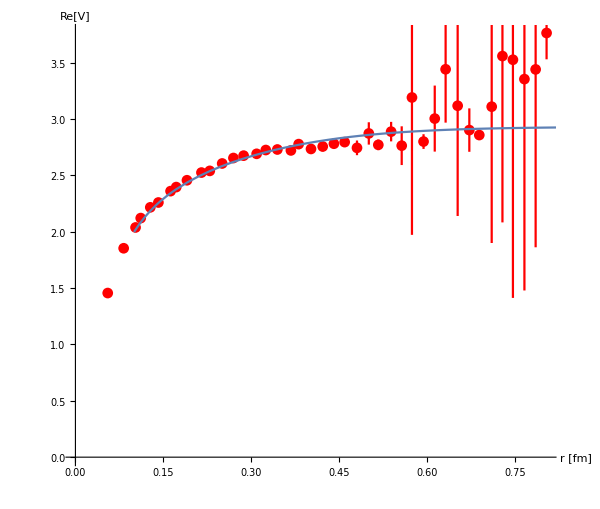

```mathematica
Block[{n=7},Show[ErrorListPlot[ReVdataTe[n],PlotStyle->Red,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600}],Plot[ReVo[r/0.197,mdfitrandfinal[[n,1]],T0constfit[[1]][β[[n]]],T0constfit[[2]][β[[n]]],T0constfit[[3]][β[[n]]]],{r,0.1,1}]]]
```

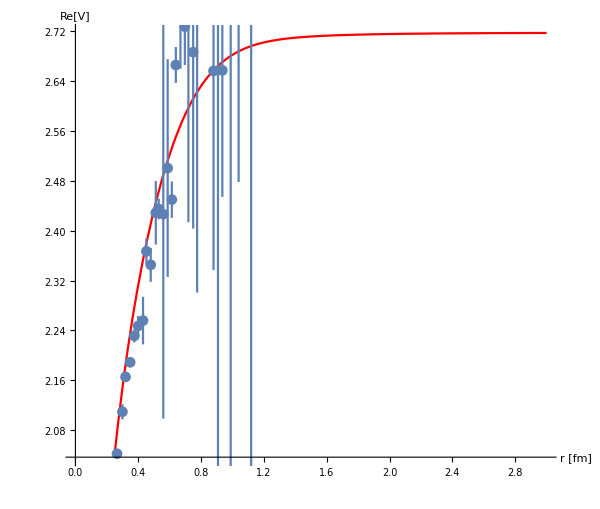

```mathematica
Block[{n=4},Show[Plot[ReVo[r/0.197,mdfitrandfinal[[n,1]],T0constfit[[1]][β[[n]]],T0constfit[[2]][β[[n]]],T0constfit[[3]][β[[n]]]],{r,0,3},PlotStyle->Red,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600}],ErrorListPlot[ReVdataTe[n]]]]
```

## Combining into single figure

### Real Part

```mathematica
β1={6.9,7.48,6.8,6.9,7,7.125,7.25,7.3,7.48};
```

```mathematica
αcontβ1=Table[T0constfit[[1]][β1[[i]]],{i,1,Length[β1]}]
```

{0.471242,0.372697,0.488233,0.471242,0.454252,0.433014,0.411775,0.40328,0.372697}

```mathematica
σcontβ1=Table[T0constfit[[2]][β1[[i]]],{i,1,Length[β1]}]
```

{0.217107,0.271234,0.207775,0.217107,0.22644,0.238105,0.24977,0.254436,0.271234}

```mathematica
ccontβ1=Table[T0constfit[[3]][β1[[i]]],{i,1,Length[β1]}]
```

{1.78111,2.62876,1.63496,1.78111,1.92726,2.10994,2.29262,2.3657,2.62876}

```mathematica
TempP={"T=41MeV","T=72MeV","T=148MeV","T=164MeV","T=182MeV","T=205MeV","T=232MeV","T=243MeV","T=286MeV"};
```

```mathematica
TempP={"T=0.24T_C","T=0.42T_C","T=0.86T_C","T=0.95T_C","T=1.06T_C","T=1.19T_C","T=1.34T_C","T=1.41T_C","T=1.66T_C"};
```

```mathematica
TempP={"T≈0(β=6.9)","T≈0(β=7.48)","T=0.86T_C","T=0.95T_C","T=1.06T_C","T=1.19T_C","T=1.34T_C","T=1.41T_C","T=1.66T_C"};
```

```mathematica
For[l=1,l≤ 2,l++,PotReRescale[l]=T0data[[l]]/.{a_,b_,c_}:>{a,b-ccontβ1[[l]]-0.45*If[l==1,0,l]+6.,c}];
```

```mathematica
For[l=1,l≤ 5,l++,PotReRescale[l+2]=ReVdataTe[l]/.{a_,b_,c_}:>{a,b-ccontβ1[[l+2]]-0.45l+5.,c}];
```

```mathematica
For[l=6,l≤ 7,l++,PotReRescale[l+2]=ReVdataTe[l][[;;-14]]/.{a_,b_,c_}:>{a,b-ccontβ1[[l+2]]-0.45 l+5.,c}];
```

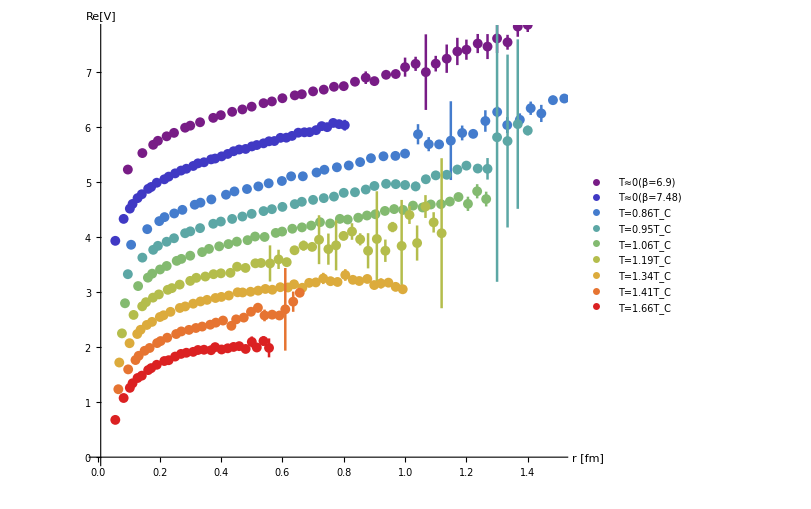

```mathematica
ReVdatPlot=ErrorListPlot[Table[PotReRescale[l],{l,1,9}],PlotRange->{{0.00001,1.5},{0.,7.7}},PlotStyle->Thread@{AbsolutePointSize[7.1],AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[0,1,1/8]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},PlotLegends->Placed[PointLegend[TempP, LegendMarkerSize->8,LegendLayout->{"Row",3}],{0.66,0.12}],AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600}]
```

```mathematica
ReVplot=Join[Table[ReVm00[r/0.197327,αcontβ1[[l]],σcontβ1[[l]],ccontβ1[[l]]]-ccontβ1[[l]]-0.45*If[l==1,0,l]+6.,{l,1,2}],Table[ReVo[r/0.197327,mdfitrandfinal[[l,1]],αcontβ1[[l+2]],σcontβ1[[l+2]],ccontβ1[[l+2]]]-ccontβ1[[l+2]]-0.45l+5.,{l,1,7}]];
```

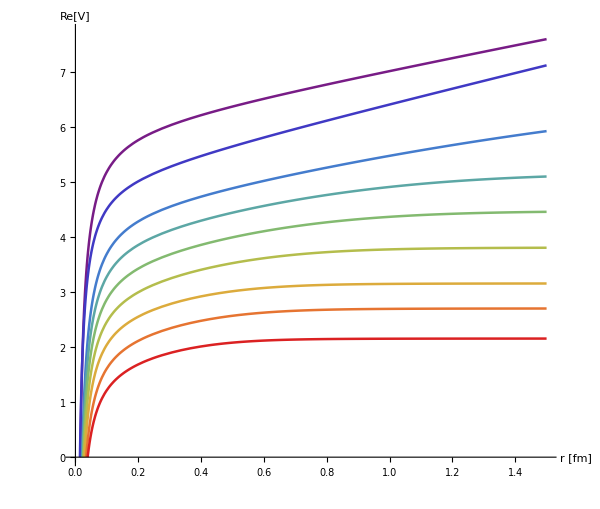

```mathematica
ReVanPlot=Plot[ReVplot,{r,0.001,1.5},PlotRange->{{0.00001,1.5},{0.,7.7}},PlotStyle->Thread@{AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[0,1,1/8]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600},PlotRange->{{0,1.5},All}]
```

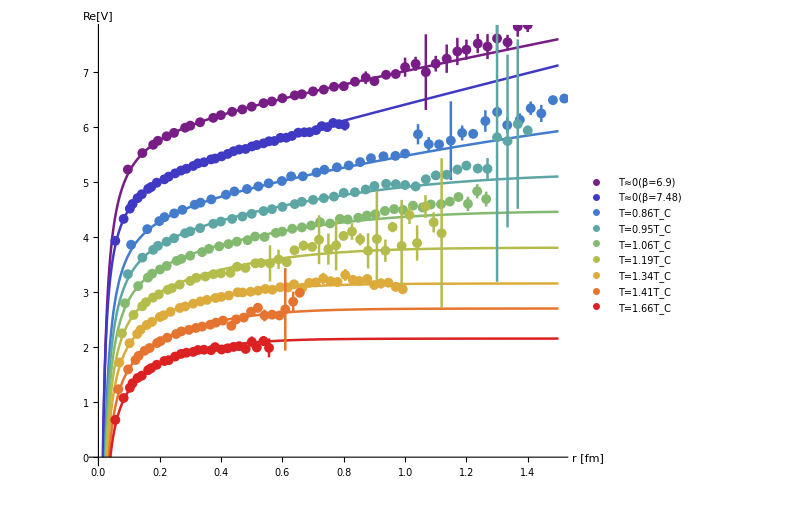

```mathematica
Show[{ReVanPlot,ReVdatPlot}]
```

```mathematica
αecontβ1=Table[T0errfit[[1]][β1[[i]]],{i,1,Length[β1]}]
```

{0.0420996,0.0123713,0.0472251,0.0420996,0.036974,0.030567,0.0241601,0.0215973,0.0123713}

```mathematica
σecontβ1=Table[T0errfit[[2]][β1[[i]]],{i,1,Length[β1]}]
```

{0.0129385,0.0120751,0.0130873,0.0129385,0.0127896,0.0126035,0.0124175,0.012343,0.0120751}

```mathematica
cecontβ1=Table[T0errfit[[3]][β1[[i]]],{i,1,Length[β1]}]
```

{0.0500451,0.0266216,0.0540837,0.0500451,0.0460066,0.0409584,0.0359103,0.033891,0.0266216}

```mathematica
ReVe[r_,l_,a_]:=ReVo[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],ccontβ1[[l+2]]]-ccontβ1[[l+2]]-0.45l+5.;
```

```mathematica
ReV0e[r_,l_,a_]:=ReVm00[r/0.197327,αcontβ1[[l]]-a αecontβ1[[l]],σcontβ1[[l]]+a σecontβ1[[l]],ccontβ1[[l]]+a cecontβ1[[l]]]-ccontβ1[[l]]-0.45*If[l==1,0,l]+6.;
```

```mathematica
TempP={"T=41MeV","T=72MeV","T=148MeV","T=164MeV","T=182MeV","T=205MeV","T=232MeV","T=243MeV","T=286MeV"};
```

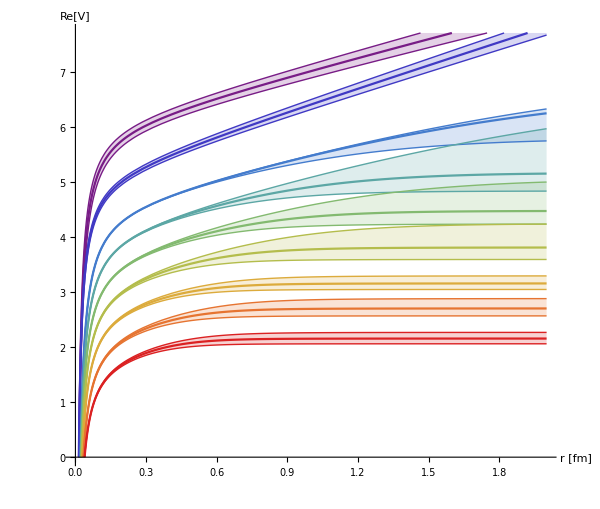

```mathematica
ReVanPlotError=Plot[{ReV0e[r,1,0],ReV0e[r,1,1],ReV0e[r,1,-1],ReV0e[r,2,0],ReV0e[r,2,1],ReV0e[r,2,-1],ReVe[r,1,0],ReVe[r,1,1],ReVe[r,1,-1],ReVe[r,2,0],ReVe[r,2,1],ReVe[r,2,-1],ReVe[r,3,0],ReVe[r,3,1],ReVe[r,3,-1],ReVe[r,4,0],ReVe[r,4,1],ReVe[r,4,-1],ReVe[r,5,0],ReVe[r,5,1],ReVe[r,5,-1],ReVe[r,6,0],ReVe[r,6,1],ReVe[r,6,-1],ReVe[r,7,0],ReVe[r,7,1],ReVe[r,7,-1]},{r,0.001,2},PlotRange->{{0.00001,2},{0.,7.7}},PlotStyle->{RGBColor[0.471412, 0.108766, 0.527016],{RGBColor[0.471412, 0.108766, 0.527016],Thin},{RGBColor[0.471412, 0.108766, 0.527016],Thin},RGBColor[0.250728, 0.225386, 0.769152],{RGBColor[0.250728, 0.225386, 0.769152],Thin},{RGBColor[0.250728, 0.225386, 0.769152],Thin},RGBColor[0.266122, 0.486664, 0.802529],{RGBColor[0.266122, 0.486664, 0.802529],Thin},{RGBColor[0.266122, 0.486664, 0.802529],Thin},RGBColor[0.36048, 0.655759, 0.645692],{RGBColor[0.36048, 0.655759, 0.645692],Thin},{RGBColor[0.36048, 0.655759, 0.645692],Thin},RGBColor[0.513417, 0.72992, 0.440682],{RGBColor[0.513417, 0.72992, 0.440682],Thin},{RGBColor[0.513417, 0.72992, 0.440682],Thin},RGBColor[0.705038, 0.742591, 0.299167],{RGBColor[0.705038, 0.742591, 0.299167],Thin},{RGBColor[0.705038, 0.742591, 0.299167],Thin},RGBColor[0.863512, 0.670771, 0.236564],{RGBColor[0.863512, 0.670771, 0.236564],Thin},{RGBColor[0.863512, 0.670771, 0.236564],Thin},RGBColor[0.902853, 0.453964, 0.192014],{RGBColor[0.902853, 0.453964, 0.192014],Thin},{RGBColor[0.902853, 0.453964, 0.192014],Thin},RGBColor[0.857359, 0.131106, 0.132128],{RGBColor[0.857359, 0.131106, 0.132128],Thin},{RGBColor[0.857359, 0.131106, 0.132128],Thin}},Filling->Flatten[Table[{i->{i+1},i->{i+2}},{i,1,27,3}]],AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600},PlotRange->{{0,1.5},All}]
```

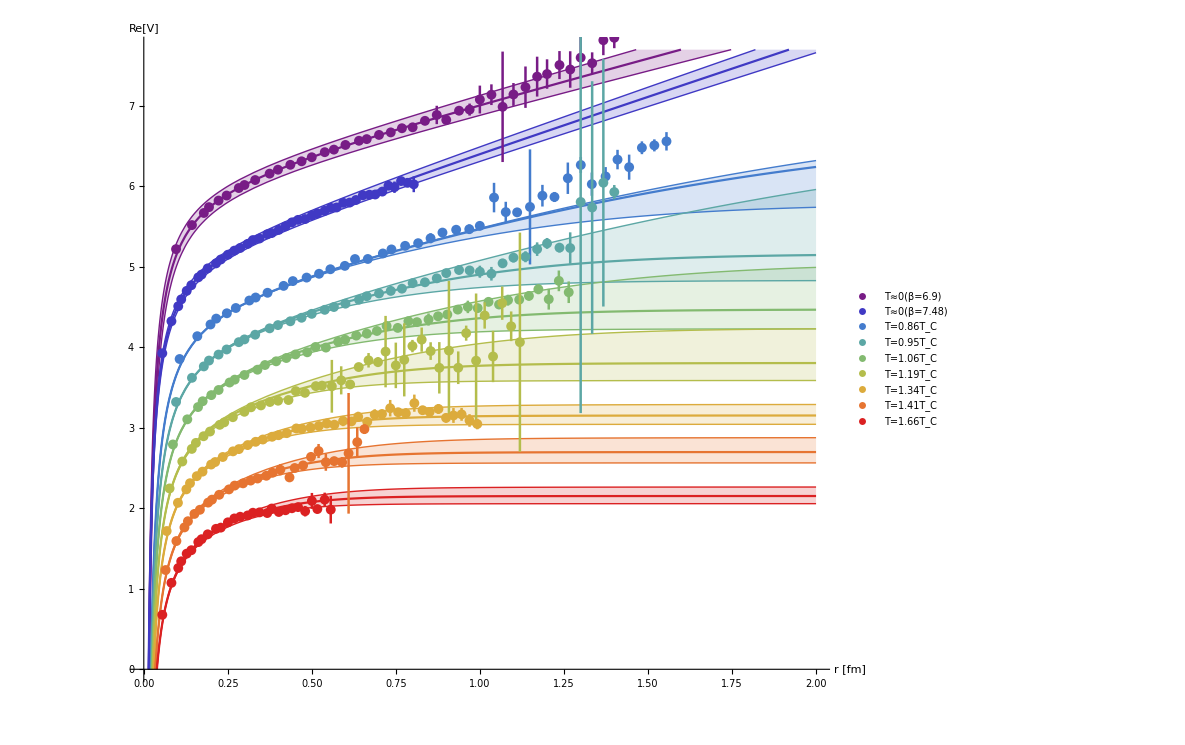

```mathematica
Show[{ReVanPlotError,ReVdatPlot}]
```

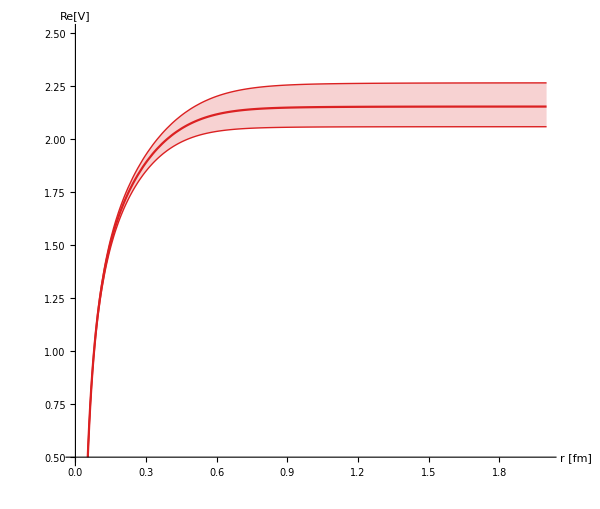

```mathematica
ReVoldPlot=Plot[{ReVe[r,7,0],ReVe[r,7,1],ReVe[r,7,-1]},{r,0.001,2},BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600},PlotRange->{0.5,2.5},PlotStyle->{RGBColor[0.857359, 0.131106, 0.132128],{RGBColor[0.857359, 0.131106, 0.132128],Thin},{RGBColor[0.857359, 0.131106, 0.132128],Thin}},Filling->{{1->{2}},{1->{3}}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black]]
```

### Imag Part

```mathematica
Shift=1.
```

1.

```mathematica
For[l=1,l≤ 7,l++,PotImRescale[l]=ImVdataTe[l]/.{a_,b_,c_}:>{a-Shift*l+7*Shift,b,c}];
```

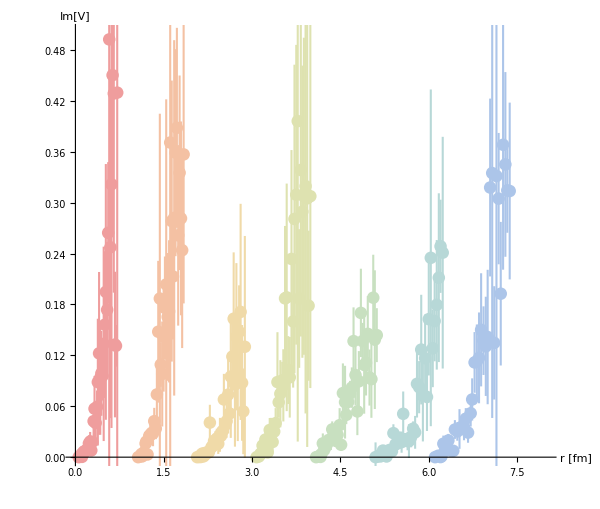

```mathematica
ImVdatPlot=ErrorListPlot[Table[PotImRescale[l][[1;;Floor[Length[PotImRescale[l]]*0.9]]],{l,1,7}],PlotRange->{{0,8},{0,0.5}},PlotStyle->Thread@{AbsolutePointSize[9],AbsoluteThickness[1.5],Lighter[Lighter[ColorData["Rainbow"]/@Range[2/8,1,1/8]]]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->16},AspectRatio->0.85,PlotRange->{0,0.35},AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

```mathematica
ImVe[1,0]=Block[{l=1,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[1,1]=Block[{l=1,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[1,-1]=Block[{l=1,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,1/1000,αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[2,0]=Block[{l=2,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,3,1/100}]];
ImVe[2,1]=Block[{l=2,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,3,1/100}]];
ImVe[2,-1]=Block[{l=2,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,3,1/100}]];
ImVe[3,0]=Block[{l=3,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,4,1/100}]];
ImVe[3,1]=Block[{l=3,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,4,1/100}]];
ImVe[3,-1]=Block[{l=3,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,4,1/100}]];
ImVe[4,0]=Block[{l=4,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,5,1/100}]];
ImVe[4,1]=Block[{l=4,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,5,1/100}]];
ImVe[4,-1]=Block[{l=4,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,5,1/100}]];
ImVe[5,0]=Block[{l=5,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,6,1/100}]];
ImVe[5,1]=Block[{l=5,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,6,1/100}]];
ImVe[5,-1]=Block[{l=5,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,6,1/100}]];
ImVe[6,0]=Block[{l=6,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,7,1/100}]];
ImVe[6,1]=Block[{l=6,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,7,1/100}]];
ImVe[6,-1]=Block[{l=6,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,7,1/100}]];
ImVe[7,0]=Block[{l=7,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,8,1/100}]];
ImVe[7,1]=Block[{l=7,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,8,1/100}]];
ImVe[7,-1]=Block[{l=7,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,8,1/100}]];
```

```mathematica
TempP2={"T=0.86T_C","T=0.95T_C","T=1.06T_C","T=1.19T_C","T=1.34T_C","T=1.41T_C","T=1.66T_C"};
```

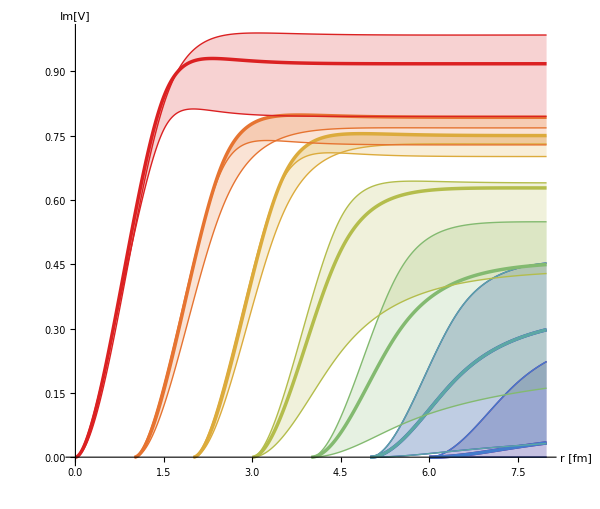

```mathematica
ImVanPlotError=ListPlot[{ImVe[1,0],ImVe[1,1],ImVe[1,-1],ImVe[2,0],ImVe[2,1],ImVe[2,-1],ImVe[1,0],ImVe[1,1],ImVe[1,-1],ImVe[2,0],ImVe[2,1],ImVe[2,-1],ImVe[3,0],ImVe[3,1],ImVe[3,-1],ImVe[4,0],ImVe[4,1],ImVe[4,-1],ImVe[5,0],ImVe[5,1],ImVe[5,-1],ImVe[6,0],ImVe[6,1],ImVe[6,-1],ImVe[7,0],ImVe[7,1],ImVe[7,-1]},Joined->True,PlotStyle->{{RGBColor[0.471412, 0.108766, 0.527016],AbsoluteThickness[2.5]},{RGBColor[0.471412, 0.108766, 0.527016],Thin},{RGBColor[0.471412, 0.108766, 0.527016],Thin},{RGBColor[0.250728, 0.225386, 0.769152],AbsoluteThickness[2.5]},{RGBColor[0.250728, 0.225386, 0.769152],Thin},{RGBColor[0.250728, 0.225386, 0.769152],Thin},{RGBColor[0.266122, 0.486664, 0.802529],AbsoluteThickness[2.5]},{RGBColor[0.266122, 0.486664, 0.802529],Thin},{RGBColor[0.266122, 0.486664, 0.802529],Thin},{RGBColor[0.36048, 0.655759, 0.645692],AbsoluteThickness[2.5]},{RGBColor[0.36048, 0.655759, 0.645692],Thin},{RGBColor[0.36048, 0.655759, 0.645692],Thin},{RGBColor[0.513417, 0.72992, 0.440682],AbsoluteThickness[2.5]},{RGBColor[0.513417, 0.72992, 0.440682],Thin},{RGBColor[0.513417, 0.72992, 0.440682],Thin},{RGBColor[0.705038, 0.742591, 0.299167],AbsoluteThickness[2.5]},{RGBColor[0.705038, 0.742591, 0.299167],Thin},{RGBColor[0.705038, 0.742591, 0.299167],Thin},{RGBColor[0.863512, 0.670771, 0.236564],AbsoluteThickness[2.5]},{RGBColor[0.863512, 0.670771, 0.236564],Thin},{RGBColor[0.863512, 0.670771, 0.236564],Thin},{RGBColor[0.902853, 0.453964, 0.192014],AbsoluteThickness[2.5]},{RGBColor[0.902853, 0.453964, 0.192014],Thin},{RGBColor[0.902853, 0.453964, 0.192014],Thin},{RGBColor[0.857359, 0.131106, 0.132128],AbsoluteThickness[2.5]},{RGBColor[0.857359, 0.131106, 0.132128],Thin},{RGBColor[0.857359, 0.131106, 0.132128],Thin}},Filling->Flatten[Table[{i->{i+1},i->{i+2}},{i,1,27,3}]],AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

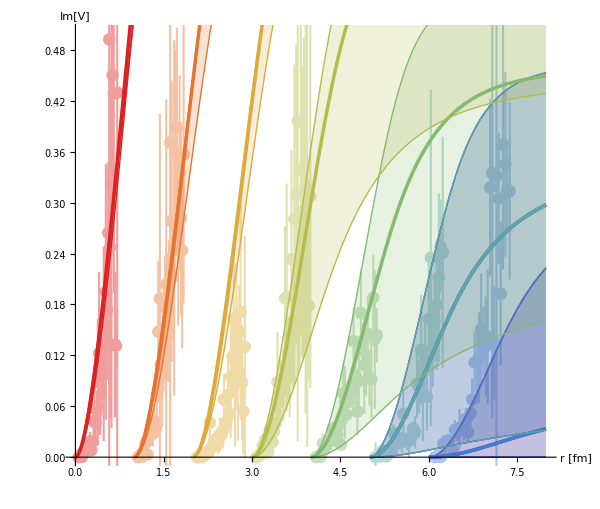

```mathematica
Show[ImVdatPlot,ImVanPlotError]
```

```mathematica
ImVe[1,0]=Block[{l=1,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[1,1]=Block[{l=1,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[1,-1]=Block[{l=1,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,1/1000,αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[2,0]=Block[{l=2,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,3,1/100}]];
ImVe[2,1]=Block[{l=2,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,3,1/100}]];
ImVe[2,-1]=Block[{l=2,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,3,1/100}]];
ImVe[3,0]=Block[{l=3,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,4,1/100}]];
ImVe[3,1]=Block[{l=3,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,4,1/100}]];
ImVe[3,-1]=Block[{l=3,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,4,1/100}]];
ImVe[4,0]=Block[{l=4,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,5,1/100}]];
ImVe[4,1]=Block[{l=4,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,5,1/100}]];
ImVe[4,-1]=Block[{l=4,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,5,1/100}]];
ImVe[5,0]=Block[{l=5,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,6,1/100}]];
ImVe[5,1]=Block[{l=5,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,6,1/100}]];
ImVe[5,-1]=Block[{l=5,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,6,1/100}]];
ImVe[6,0]=Block[{l=6,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,7,1/100}]];
ImVe[6,1]=Block[{l=6,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,7,1/100}]];
ImVe[6,-1]=Block[{l=6,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,7,1/100}]];
ImVe[7,0]=Block[{l=7,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,8,1/100}]];
ImVe[7,1]=Block[{l=7,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,8,1/100}]];
ImVe[7,-1]=Block[{l=7,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsb[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,8,1/100}]];
```

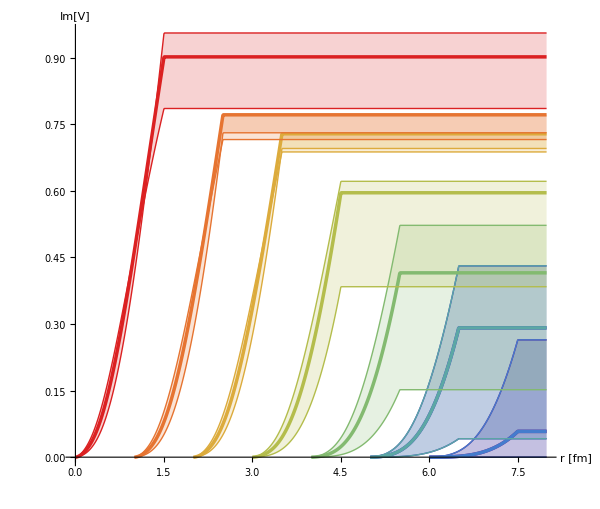

```mathematica
ImVanPlotError=ListPlot[{ImVe[1,0],ImVe[1,1],ImVe[1,-1],ImVe[2,0],ImVe[2,1],ImVe[2,-1],ImVe[1,0],ImVe[1,1],ImVe[1,-1],ImVe[2,0],ImVe[2,1],ImVe[2,-1],ImVe[3,0],ImVe[3,1],ImVe[3,-1],ImVe[4,0],ImVe[4,1],ImVe[4,-1],ImVe[5,0],ImVe[5,1],ImVe[5,-1],ImVe[6,0],ImVe[6,1],ImVe[6,-1],ImVe[7,0],ImVe[7,1],ImVe[7,-1]},Joined->True,PlotStyle->{{RGBColor[0.471412, 0.108766, 0.527016],AbsoluteThickness[2.5]},{RGBColor[0.471412, 0.108766, 0.527016],Thin},{RGBColor[0.471412, 0.108766, 0.527016],Thin},{RGBColor[0.250728, 0.225386, 0.769152],AbsoluteThickness[2.5]},{RGBColor[0.250728, 0.225386, 0.769152],Thin},{RGBColor[0.250728, 0.225386, 0.769152],Thin},{RGBColor[0.266122, 0.486664, 0.802529],AbsoluteThickness[2.5]},{RGBColor[0.266122, 0.486664, 0.802529],Thin},{RGBColor[0.266122, 0.486664, 0.802529],Thin},{RGBColor[0.36048, 0.655759, 0.645692],AbsoluteThickness[2.5]},{RGBColor[0.36048, 0.655759, 0.645692],Thin},{RGBColor[0.36048, 0.655759, 0.645692],Thin},{RGBColor[0.513417, 0.72992, 0.440682],AbsoluteThickness[2.5]},{RGBColor[0.513417, 0.72992, 0.440682],Thin},{RGBColor[0.513417, 0.72992, 0.440682],Thin},{RGBColor[0.705038, 0.742591, 0.299167],AbsoluteThickness[2.5]},{RGBColor[0.705038, 0.742591, 0.299167],Thin},{RGBColor[0.705038, 0.742591, 0.299167],Thin},{RGBColor[0.863512, 0.670771, 0.236564],AbsoluteThickness[2.5]},{RGBColor[0.863512, 0.670771, 0.236564],Thin},{RGBColor[0.863512, 0.670771, 0.236564],Thin},{RGBColor[0.902853, 0.453964, 0.192014],AbsoluteThickness[2.5]},{RGBColor[0.902853, 0.453964, 0.192014],Thin},{RGBColor[0.902853, 0.453964, 0.192014],Thin},{RGBColor[0.857359, 0.131106, 0.132128],AbsoluteThickness[2.5]},{RGBColor[0.857359, 0.131106, 0.132128],Thin},{RGBColor[0.857359, 0.131106, 0.132128],Thin}},Filling->Flatten[Table[{i->{i+1},i->{i+2}},{i,1,27,3}]],AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

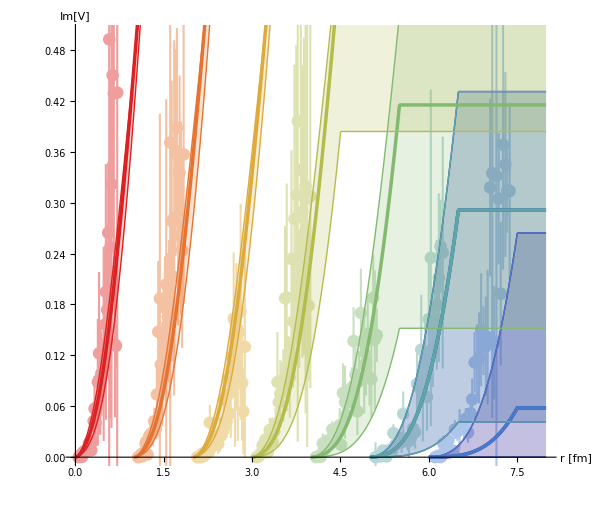

```mathematica
Show[ImVdatPlot,ImVanPlotError]
```